# Blatt 5 - Optimierung der Emittanz im DBA-Lattice

Jonas Neundorf & Jan Skottke

Definiere Konstanten

```mathematica
constants={c-> 3.*10^8, q-> 1.602*10^-19,m-> 0.511*10^-3,r0-> 2.818*10^-15,cq-> 3.8*10^-13};
```

Du kannst η mit “Esc h Esc” schreiben (dann musst du nicht immer “Esc et Esc” benutzten)
Und das geschwungene ℋ kannst du mit “Esc scH Esc” machen.

## Vorbereitungen

#### Berechnung der Dispersionfunktion

Definiere die Matritzen für die Magnete:

```mathematica
mF[f_]:={{1,0,0},{-1/f,1,0},{0,0,1}} (*fokussierender Quad*)
```

```mathematica
mD[s_, ρ_] := {{Cos[s/ρ], ρ*Sin[s/ρ], ρ*(1 - Cos[s/ρ])}, {-1/ρ*Sin[s/ρ], Cos[s/ρ], Sin[s/ρ]}, {0, 0, 1}}(*Dipol*)
```

Definiere Dispersionsfunktionen:

```mathematica
η[s_]:=ρ*(1-Cos[s/ρ])
```

```mathematica
dη[s_]=D[η[s],s];
```

Bestimme f:

```mathematica
eq={0,0,1}==mD[s,ρ].mF[f].mD[s,ρ].{η[0],dη[0],1}//FullSimplify (*Dispersion nach dem ersten Dipol*)
```

{0,0,1}=={(ρ (2 f-2 f Cos[(2 s)/ρ]-2 ρ Sin[s/ρ]+ρ Sin[(2 s)/ρ]))/(2 f),(Cos[s/ρ] (ρ (-1+Cos[s/ρ])+2 f Sin[s/ρ]))/f,1}

```mathematica
focus=Solve[eq,f]//Flatten
```

{f→1/2 ρ Tan[s/(2 ρ)]}

Diese Brennweite muss der Quadropol haben, damit die Dispersion am Ende wieder bei {0,0,1} ist.

#### Tests

Die berechnete Brennweite liefert das gewünschte Ergebnis, dass die Dispersion nach dem 2. Dipol wieder bei {0,0,1} ist.

```mathematica
mD[s,ρ].mF[f].mD[s,ρ].{η[0],dη[0],1}//.focus//FullSimplify
```

{0,0,1}

Dispersion nach dem ersten Dipol:

```mathematica
dispd1=mD[s,ρ].{η[0],dη[0],1}//FullSimplify
```

{ρ-ρ Cos[s/ρ],Sin[s/ρ],1}

Dispersion nach dem Quadropol und dem zweiten Dipol: (Hier gehen wir nur davon aus, dass der Startpunkt im Quadropol liegt und NICHT im 1. Dipol, da die Dispersion nach dem Quadropol und 2. Dipol ja {η,-dη} sein sollte. Und das ist sie!! :))

```mathematica
dispqd2=mF[f].mD[s,ρ].{η[0],dη[0],1}//.focus//FullSimplify
```

{ρ-ρ Cos[s/ρ],-Sin[s/ρ],1}

KOMMENTAR: Ab hier wollte ich eigentlich einen piecewise plot machen, damit man sieht wie die Dispersion verläuft (wie auf dem Blatt gefordert), aber leider bin ich zu blöd dafür T_T

```mathematica
dispersion[s_]={{{1,0,0},{0,1,0},{0,0,1}},mD[s,ρ].mF[f],mD[L,ρ].mF[f].mD[s,ρ]}.{η[0],dη[0],1}//.focus//FullSimplify
```

{{0,0,1},{ρ-ρ Cos[s/ρ],Sin[s/ρ],1},{ρ-ρ Cos[(L-s)/ρ],Sin[(L-s)/ρ],1}}

```mathematica
fullη[s_]=Piecewise[{{dispersion[s][[2,1]], s≤ L}, {dispersion[s-L][[3,1]], L≤ s≤2*L}}]
```

Piecewise[{{ρ-ρ Cos[s/ρ], s≤L}, {ρ-ρ Cos[(2 L-s)/ρ], L≤s≤2 L}, {0, True}}]

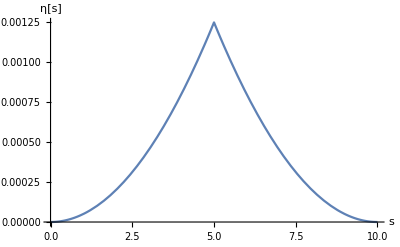

```mathematica
Plot[fullη[x]//.focus//.{L ->5, ρ-> 10000}, {x, 0, 10}, AxesLabel-> {"s", "η[s]"}]
```

Hier wird dη geplottet:

```mathematica
fulldη[s_]=Piecewise[{{dispersion[s][[2,2]], s ≤ L}, {dispersion[s-L][[3,2]], L≤ s≤2*L}}]
```

Piecewise[{{Sin[s/ρ], s≤L}, {Sin[(2 L-s)/ρ], L≤s≤2 L}, {0, True}}]

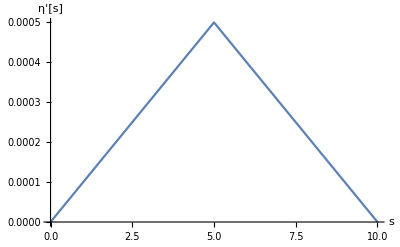

```mathematica
Plot[fulldη[x]//.focus//.{L ->5, ρ-> 10000}, {x, 0, 10}, AxesLabel-> {"s", "η'[s]"}]
```

#### Berechnung der Twiss Parameter (β-Funktionen)

```mathematica
bmat={{β0,-α0},{-α0,γ0}}
```

{{β0,-α0},{-α0,γ0}}

```mathematica
drift[s_]:={{1,s},{0,1}}
```

```mathematica
quad[f_]:={{1,0},{-1/f,1}}
```

Zuerst berechnen wir die Parameter für den ersten Dipol:

```mathematica
twissd1[s_]=drift[s].bmat.Transpose[drift[s]]//FullSimplify
```

{{-2 s α0+β0+s^2 γ0,-α0+s γ0},{-α0+s γ0,γ0}}

Nun zur Berechnung der Twissparameter für den letzten Teil, also für den Quadropol und dem zweiten Dipol: (Kommentar: Wenn ich mich richtig erinnere dann müsste folgendes gelten: B_1 = M * B_0 * M^T(das steht so im Skript) und weiter sollte gelten (das habe ich nicht im Skript gefunden): 
B_2 = M * B_1 * M^T= M * (M * B_0 * M^T) * M^T; wenn das nicht richtig ist, musst du ab hier einiges korrigieren :( )

```mathematica
twissqd2[s_]=drift[s].(quad[f].bmat.Transpose[quad[f]]).Transpose[drift[s]]//.focus//FullSimplify
```

{{-2 s α0+β0+s^2 γ0+(4 s Cot[s/(2 ρ)] (s α0 ρ-β0 ρ+s β0 Cot[s/(2 ρ)]))/ρ^2,-α0+s γ0+(2 Cot[s/(2 ρ)] (2 s α0 ρ-β0 ρ+2 s β0 Cot[s/(2 ρ)]))/ρ^2},{-α0+s γ0+(2 Cot[s/(2 ρ)] (2 s α0 ρ-β0 ρ+2 s β0 Cot[s/(2 ρ)]))/ρ^2,γ0+(4 Cot[s/(2 ρ)] (α0 ρ+β0 Cot[s/(2 ρ)]))/ρ^2}}

```mathematica
β[s_]=Piecewise[{{twissd1[s][[1,1]], s≤ L}, {twissqd2[s-L][[1,1]], L≤ s≤2*L}}]
```

Piecewise[{{-2 s α0+β0+s^2 γ0, s≤L}, {-2 (-L+s) α0+β0+(-L+s)^2 γ0+(4 (-L+s) Cot[(-L+s)/(2 ρ)] ((-L+s) α0 ρ-β0 ρ+(-L+s) β0 Cot[(-L+s)/(2 ρ)]))/ρ^2, L≤s≤2 L}, {0, True}}]

```mathematica
α[s_]=Piecewise[{{-twissd1[s][[1,2]], s≤ L}, {-twissqd2[s-L][[1,2]], L≤ s≤2*L}}]
```

Piecewise[{{α0-s γ0, s≤L}, {α0-(-L+s) γ0-(2 Cot[(-L+s)/(2 ρ)] (2 (-L+s) α0 ρ-β0 ρ+2 (-L+s) β0 Cot[(-L+s)/(2 ρ)]))/ρ^2, L≤s≤2 L}, {0, True}}]

```mathematica
γ[s_]=Piecewise[{{twissd1[s][[2,2]], s<=L}, {twissqd2[s-L][[2,2]], L≤ s≤2*L}}]
```

Piecewise[{{γ0, s≤L}, {γ0+(4 Cot[(-L+s)/(2 ρ)] (α0 ρ+β0 Cot[(-L+s)/(2 ρ)]))/ρ^2, L≤s≤2 L}, {0, True}}]

#### Berechnung der Funktion ℋ

Als Hinweis: das eigentliche η in der Gleichung (siehe Aufgabenblatt) wird hier durch fullη und η' wird durch fulldη ersetzt. Falls dir ein besserer Name dafür einfällt, kannst du das gerne ändern. :D

```mathematica
ℋ[s_]:=γ[s]*(fullη[s])^2+2*α[s]*fullη[s]*fulldη[s]+β[s]*(fulldη[s])^2
```

## Berechnung und Optimierung der Emittanz

```mathematica
para={ρ-> L/θ,L-> 1.96, θ-> 0.0984,γrel-> 6000/0.511};(*θ->L/ρ*)
```

```mathematica
parastart={γ0-> (1+α0^2)/β0,β0-> 2*√(3/5)*L,α0-> √15}; (*Bei γ0 bin ich mir nicht 100%ig sicher ob man das so machen darf, aber mir ist nichts besseres eingefallen*)
```

#### Die Twiss-Parameter

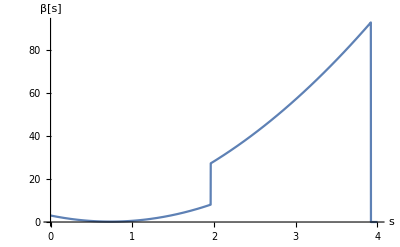

```mathematica
Plot[β[x]//.focus//.parastart//.para, {x, 0, 4}, AxesLabel-> {"s", "β[s]"}] (*keine Ahnung was ich dazu sagen soll oder was mir da auffällt, vielleicht habe ich auch i.wo einen Fehler gemacht, was nicht so unwahrscheinlich ist....*)
```

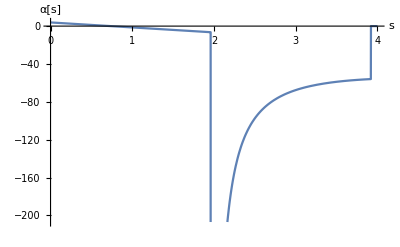

```mathematica
Plot[α[x]//.focus//.parastart//.para, {x, 0, 4}, AxesLabel-> {"s", "α[s]"}]
```

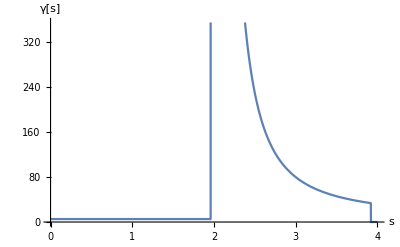

```mathematica
Plot[γ[x]//.focus//.parastart//.para, {x, 0, 4}, AxesLabel-> {"s", "γ[s]"}]
```

#### Die Funktion ℋ

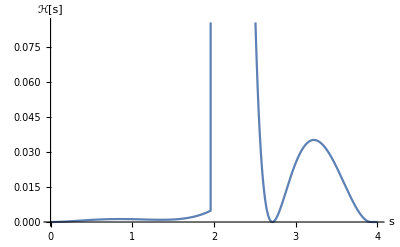

```mathematica
Plot[ℋ[x]//.focus//.parastart//.para, {x, 0, 4}, AxesLabel-> {"s", "ℋ[s]"}]
```

#### Richtige Optimierung

```mathematica
numH=ℋ[s]//.para//.focus//.γ0-> (1+α0^2)/β0;//FullSimplify
```

```mathematica
intH=Integrate[numH,{s,0,L}]//.para//FullSimplify (*Diese Integration sollte schon falsch sein, da diese nur über einen Dipol laufen würde. Wie du weiter unten siehst, liefert die Integration über beide Dipole leider kein Ergebnis. Ich weiß leider nicht wie ich das beheben kann. *)
```

Integrate::pwrl: Unable to prove that integration limits {0,L} are real. Adding assumptions may help.

-0.00927415 α0+(0.00363267+0.00363267 α0^2)/β0+0.0063137 β0

```mathematica
nsβ=Solve[D[intH,β0]==0,β0]//FullSimplify (*da β0>0 sein soll, muss man die 2. Lösung nehmen*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{β0→-2.424×10^-8 √(9.79211×10^14+9.79211×10^14 α0^2)},{β0→2.424×10^-8 √(9.79211×10^14+9.79211×10^14 α0^2)}}

```mathematica
nsα=Solve[D[intH,α0]==0,α0]//FullSimplify//Flatten
```

{α0→1.27649 β0}

```mathematica
test=Integrate[numH//.ρ-> L/θ,{s,0,2*L}]//.para//FullSimplify
```

Integrate::pwrl: Unable to prove that integration limits {0,2 L} are real. Adding assumptions may help.

∫_0^3.92 ((Piecewise[{{(1+α0^2)/β0, s≤1.96}, {(1+α0^2)/β0+0.0100818 Cot[0.025102 (-1.96+s)] (19.9187 α0+β0 Cot[0.025102 (-1.96+s)]), 1.96≤s≤3.92}, {0, True}}]) (Piecewise[{{19.9187-19.9187 Cos[0.0502041 s], s≤1.96}, {19.9187-19.9187 Cos[0.1968-0.0502041 s], 1.96≤s≤3.92}, {0, True}}])^2+(Piecewise[{{Sin[0.0502041 s], s≤1.96}, {Sin[0.1968-0.0502041 s], 1.96≤s≤3.92}, {0, True}}]) (2 (Piecewise[{{α0-(s (1+α0^2))/β0, s≤1.96}, {α0-((-1.96+s) (1+α0^2))/β0-0.0050409 Cot[0.025102 (-1.96+s)] (39.8374 (-1.96+s) α0-19.9187 β0+2 (-1.96+s) β0 Cot[0.025102 (-1.96+s)]), 1.96≤s≤3.92}, {0, True}}]) (Piecewise[{{19.9187-19.9187 Cos[0.0502041 s], s≤1.96}, {19.9187-19.9187 Cos[0.1968-0.0502041 s], 1.96≤s≤3.92}, {0, True}}])+(Piecewise[{{-2 s α0+(s^2 (1+α0^2))/β0+β0, s≤1.96}, {-2 (-1.96+s) α0+((-1.96+s)^2 (1+α0^2))/β0+β0+0.0100818 (-1.96+s) Cot[0.025102 (-1.96+s)] (19.9187 (-1.96+s) α0-19.9187 β0+(-1.96+s) β0 Cot[0.025102 (-1.96+s)]), 1.96≤s≤3.92}, {0, True}}]) (Piecewise[{{Sin[0.0502041 s], s≤1.96}, {Sin[0.1968-0.0502041 s], 1.96≤s≤3.92}, {0, True}}])))ⅆs